H:\Version\git\ag\FPP\SC_Models\HM_Elastica

k=0.847213

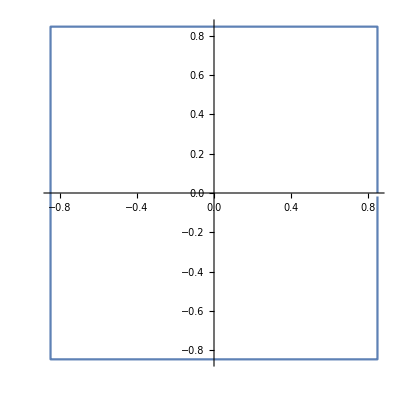

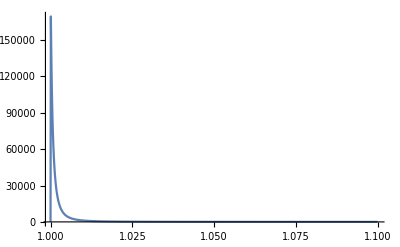

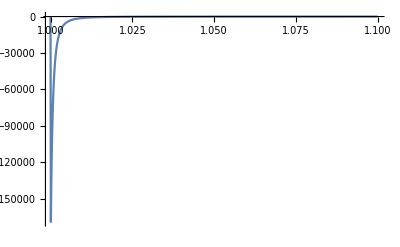

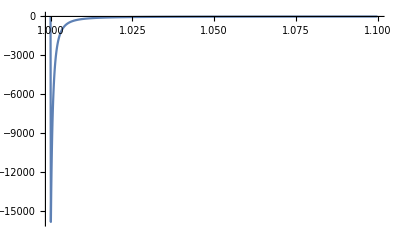

```mathematica
SetDirectory[NotebookDirectory[]]
data=ReadList["results.txt",{Number,Number, Number,Number, Number,Number,Number},RecordLists->True];
rawData=Import["results.dat"];
lineData=Import["line_results.dat"];
contour={#⟦3⟧,#⟦4⟧}&/@data⟦1⟧;
k=Max[Abs[contour]];
Print["k=",k];
cPlot=ListPlot[contour, Joined->True,AspectRatio->Automatic]
lpSSr=ListPlot[{#⟦1⟧,#⟦2⟧}&/@lineData,Joined->True,PlotRange->All]
lpSSa=ListPlot[{#⟦1⟧,#⟦3⟧}&/@lineData,Joined->True,PlotRange->All]
lpSSt=ListPlot[{#⟦1⟧,#⟦4⟧}&/@lineData,Joined->True,PlotRange->All]
```

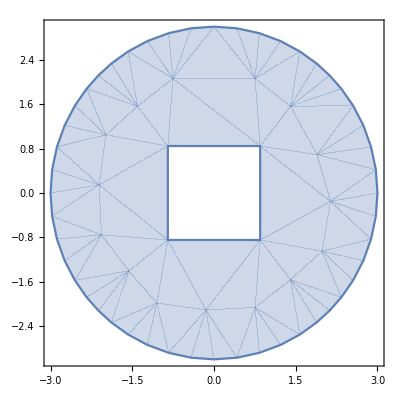

```mathematica
ssr={#⟦3⟧,#⟦4⟧,#⟦5⟧}&/@rawData;
ssa={#⟦3⟧,#⟦4⟧,#⟦6⟧}&/@rawData;
sst={#⟦3⟧,#⟦4⟧,#⟦7⟧}&/@rawData;
inPoly=Polygon[{{k,k},{-k,k},{-k,-k},{k,-k}}];
outDisk=Disk[{0,0},3];
ℛ=RegionDifference[outDisk,inPoly];
RegionPlot[ℛ]
```

```mathematica
(*
ssrPlot=ListContourPlot[ssr,PlotRange->{-4,0},RegionFunction->Function[{x,y},x≤-k || x≥k || y≤-k || y≥k],ColorFunction->Hue,Contours->30,PlotLegends->Automatic]
ssaPlot=ListContourPlot[ssa,PlotRange->{0,4},RegionFunction->Function[{x,y},x≤-k || x≥k || y≤-k || y≥k],ColorFunction->Hue,Contours->30,PlotLegends->Automatic]
Show[sstPlot,cPlot]
*)
kk=k*1.03;
sstPlot=ListContourPlot[sst,PlotRange->{-4,4},Contours->50,RegionFunction->Function[{x,y},x≤-kk || x≥kk || y≤-kk || y≥kk],ColorFunction->Hue,PlotLegends->Automatic]
Export["contour.pdf",sstPlot]
```

-Graphics-

contour.pdf

```mathematica
ListPointPlot3D[sst,PlotRange->{-4,4}]
```

-Graphics3D-

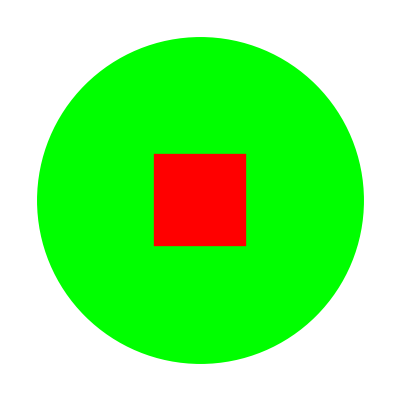

RegionDifference[Disk[{0,0},3],Polygon[{{0.847213,0.847213},{-0.847213,0.847213},{-0.847213,-0.847213},{0.847213,-0.847213}}]]

```mathematica
inPoly=Polygon[{{k,k},{-k,k},{-k,-k},{k,-k}}];
outDisk=Disk[{0,0},3];
Show[Graphics[{Green,outDisk}],Graphics[{Red,inPoly}]]
ℛ=RegionDifference[outDisk,inPoly]
```

```mathematica
RegionPlot[ℛ]
```

-Graphics-